```mathematica
ClearAll["Global`*"];
(* Dwuczłonowa rakieta o całkowitej masie mc = 1000kg została wystrzelona z wyrzutni z prędkością v0 pod kątem a=45 stopni do poziomu. W momencie, gdy pocisk znajdował się w najwyższym punkcie toru odpalenie ładunku spowodowało rozłączenie się członów rakiety i pierwszy człon spadł dokładnie w miejscu odpalenia rakiety. Wjakiej odległości od wyrzutni spadnie na ziemię drugi człon, jeżeli jego masa m2=xmc. Sporządzić wykresy dla v0=100:200m/s w dwóch przypadkach:
a) x=0.1, b) x=0.4 *)
```

```mathematica
α=45;             (* deg *)
```

```mathematica
g=9.81;         (* m/s^2 *)
```

```mathematica
vx=vo×Cos[α °]
```

vo/(√2)

```mathematica
m1=(1-x)×m;
m2=x×m;
```

```mathematica
pp=m×vx;
p1=-m1×v1;
p2=m2×v2;
```

```mathematica
A=Solve[{ p1+p2==pp,v1==vx},v2,v1]
```

Solve::bdomv: Warning: v1 is not a valid domain specification. Assuming it is a variable to eliminate.

{{v2→-(-2 √2 vo+√2 vo x)/(2 x)}}

```mathematica
zuk=(vo^2×Sin[2×α °])/g;
huk=(vo^2×Sin[α °]^2)/(2×g);
zpoz=v2×√((2×huk)/g)/.A[[1,1]]
```

-(0.0360401 √(vo^2) (-2 √2 vo+√2 vo x))/x

```mathematica
s=1/2×zuk+zpoz
```

0.0509684 vo^2-(0.0360401 √(vo^2) (-2 √2 vo+√2 vo x))/x

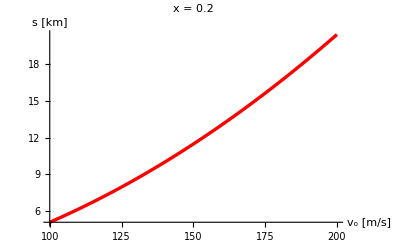

```mathematica
rys1=Plot[s×10^-3/.x->0.2,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.2  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```

### Sporzadzenie wykresu obrazujacego zaleznosc zasiegu drugiego czlonu rakiety od szybkosci poczatkowej rakiety dla x = 0.4.

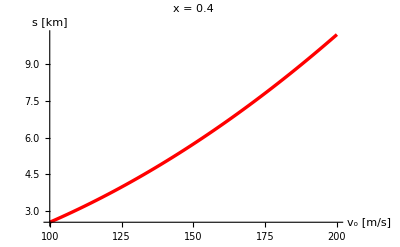

```mathematica
rys2=Plot[s×10^-3/.x->0.4,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.4  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```